## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"UTILITY_readBeamFiles.nb"}]]
```

```mathematica
fileNums = Range[0,20]
fileNames = NotebookDirectory[]<>ToString[#]<>".h5"&/@fileNums
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/0.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/1.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/2.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/3.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/4.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/5.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/6.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/7.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/8.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/9.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/10.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/11.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/12.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/13.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/14.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/15.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/16.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/17.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/18.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/19.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/20.h5}

## Process single

```mathematica
data = readBeamFile[fileNames[[1]]];
```

```mathematica
scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;
```

```mathematica
iqrRangeScale = 2;
```

```mathematica
dataRanges = {
Median[#]-iqrRangeScale*InterquartileRange[#],
Median[#]+iqrRangeScale*InterquartileRange[#]
}&/@Transpose[scaledData]
```

{{-361.597,192.013},{-794.451,505.119},{-27.867,34.9406},{-104.532,14.2961},{-54.3169,72.7184},{9.46837,10.1749}}

```mathematica
Length[scaledData]
clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];
Length[clippedData]
```

99978

86295

```mathematica
imageSize=800;
rasterSize = 800;
```

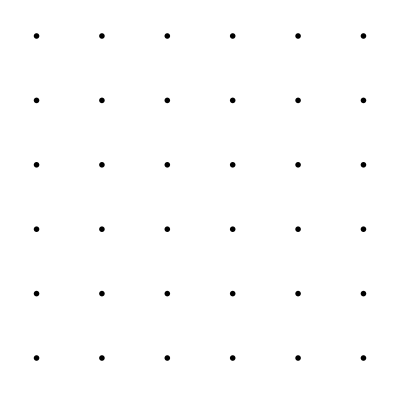

```mathematica
GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize]
],
{i,1,6},
{j,1,6}
]]
```

## Automate (hold plot ranges constant)

```mathematica
Dynamic[fileName]
imgArr = Table[
data = readBeamFile[fileName];

scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;

clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];

GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize],
ImageSize->2400
],
{i,1,6},
{j,1,6}
]],

{fileName,fileNames}
];
```

```mathematica
Export[NotebookDirectory[]<>"anim.gif",imgArr,ImageSize->2400]
```

/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - move to optimum/anim.gif